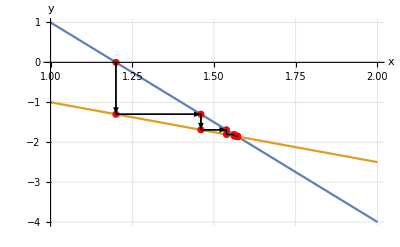

```mathematica
SetDirectory[NotebookDirectory[]];
itsZ = Import["iterationsZeidelPresentation.txt","Table"]/1.0;
itsU = Table[{itsZ[[i-1]],itsZ[[i]]},{i,2,(Length[itsZ]+1)/2}];
u = Graphics[Arrow[{{{1.2,0.},{1.2,-1.3}},{{1.2,-1.3},{1.46,-1.3}},{{1.46,-1.3},{1.46,-1.69}},{{1.46,-1.69},{1.538,-1.69}}}]];
u1 = Graphics[Line[itsU]];
lp = ListPlot[itsZ,PlotStyle->Red];
y1[x_]:=6-5x;
y2[x_]:=1/2-3/2 x;
LinearSolve[{{5.0,1},{2,3}},{{6},{1}}];
myplot = Plot[{y1[x],y2[x]},{x,1,2}];
Show[myplot,lp,u,u1,PlotRange->All,GridLines->Automatic,AxesLabel->{"x","y"}]
```